## Import

```mathematica
filepath="/home/abergman/projects/barrestin/python/StotVsMAPKpp.csv"
```

/home/abergman/projects/barrestin/python/StotVsMAPKpp.csv

```mathematica
dat=Rest@Import[filepath]
```

{{0.,0.259374},{0.01,0.333505},{0.02,0.405994},{0.03,0.476303},{0.04,0.543828},{0.05,0.607917},{0.06,0.667908},{0.07,0.723178},{0.08,0.773213},{0.09,0.817669},{0.1,0.856415},{0.11,0.889539},{0.12,0.917318},{0.13,0.940161},{0.14,0.958544},{0.15,0.972959},{0.16,0.98387},{0.17,0.991693},{0.18,0.996786},{0.19,0.999448},{0.2,0.999926},{0.21,0.998416},{0.22,0.995079},{0.23,0.99004},{0.24,0.983404},{0.25,0.975257},{0.26,0.965674},{0.27,0.95473},{0.28,0.942501},{0.29,0.929072},{0.3,0.91454},{0.31,0.899017},{0.32,0.882632},{0.33,0.865525},{0.34,0.847849},{0.35,0.829758},{0.36,0.811408},{0.37,0.792945},{0.38,0.774505},{0.39,0.756208},{0.4,0.738155},{0.41,0.72043},{0.42,0.7031},{0.43,0.686215},{0.44,0.669811},{0.45,0.653912},{0.46,0.638531},{0.47,0.623673},{0.48,0.609336},{0.49,0.595515},{0.5,0.582199},{0.51,0.569374},{0.52,0.557025},{0.53,0.545135},{0.54,0.533688},{0.55,0.522666},{0.56,0.51205},{0.57,0.501824},{0.58,0.491969},{0.59,0.48247},{0.6,0.473311},{0.61,0.464474},{0.62,0.455946},{0.63,0.447713},{0.64,0.43976},{0.65,0.432075},{0.66,0.424646},{0.67,0.41746},{0.68,0.410508},{0.69,0.403777},{0.7,0.397259},{0.71,0.390943},{0.72,0.384822},{0.73,0.378886},{0.74,0.373127},{0.75,0.367539},{0.76,0.362113},{0.77,0.356843},{0.78,0.351723},{0.79,0.346746},{0.8,0.341907},{0.81,0.337199},{0.82,0.332619},{0.83,0.32816},{0.84,0.323819},{0.85,0.31959},{0.86,0.31547},{0.87,0.311454},{0.88,0.307538},{0.89,0.303719},{0.9,0.299994},{0.91,0.296358},{0.92,0.29281},{0.93,0.289345},{0.94,0.285961},{0.95,0.282654},{0.96,0.279424},{0.97,0.276266},{0.98,0.273178},{0.99,0.270159},{1.,0.267206},{1.01,0.264316},{1.02,0.261488},{1.03,0.25872},{1.04,0.25601},{1.05,0.253356},{1.06,0.250756},{1.07,0.248209},{1.08,0.245714},{1.09,0.243268},{1.1,0.24087},{1.11,0.238519},{1.12,0.236214},{1.13,0.233952},{1.14,0.231734},{1.15,0.229557},{1.16,0.22742},{1.17,0.225324},{1.18,0.223265},{1.19,0.221244},{1.2,0.219259},{1.21,0.217309},{1.22,0.215393},{1.23,0.213512},{1.24,0.211662},{1.25,0.209845},{1.26,0.208058},{1.27,0.206302},{1.28,0.204575},{1.29,0.202877},{1.3,0.201206},{1.31,0.199563},{1.32,0.197947},{1.33,0.196357},{1.34,0.194792},{1.35,0.193251},{1.36,0.191735},{1.37,0.190243},{1.38,0.188774},{1.39,0.187327},{1.4,0.185902},{1.41,0.184499},{1.42,0.183116},{1.43,0.181755},{1.44,0.180413},{1.45,0.179091},{1.46,0.177789},{1.47,0.176505},{1.48,0.175239},{1.49,0.173992},{1.5,0.172762},{1.51,0.17155},{1.52,0.170354},{1.53,0.169175},{1.54,0.168013},{1.55,0.166866},{1.56,0.165734},{1.57,0.164618},{1.58,0.163517},{1.59,0.162431},{1.6,0.161359},{1.61,0.1603},{1.62,0.159256},{1.63,0.158225},{1.64,0.157208},{1.65,0.156204},{1.66,0.155212},{1.67,0.154233},{1.68,0.153266},{1.69,0.152311},{1.7,0.151368},{1.71,0.150437},{1.72,0.149517},{1.73,0.148608},{1.74,0.14771},{1.75,0.146823},{1.76,0.145946},{1.77,0.14508},{1.78,0.144225},{1.79,0.143379},{1.8,0.142543},{1.81,0.141717},{1.82,0.1409},{1.83,0.140093},{1.84,0.139295},{1.85,0.138506},{1.86,0.137726},{1.87,0.136954},{1.88,0.136191},{1.89,0.135437},{1.9,0.134691},{1.91,0.133953},{1.92,0.133223},{1.93,0.132501},{1.94,0.131787},{1.95,0.131081},{1.96,0.130382},{1.97,0.129691},{1.98,0.129006},{1.99,0.128329}}

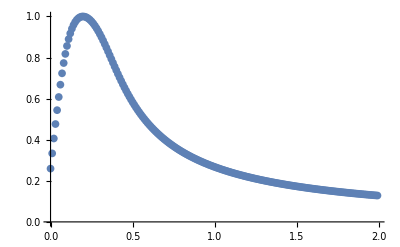

```mathematica
ListPlot[dat]
```

```mathematica
Count[dat,{x_,_}/;x<0.25]
```

25

```mathematica
Count[dat,{x_,_}/;x>0.25]
```

174

```mathematica
func=Interpolation[dat]
```

InterpolatingFunction[{{0., 1.99}}, <>]

```mathematica
xSves=Join[FindDivisions[{0,0.25},100],
FindDivisions[{0.25,2},100]//Select[#,(#>0.25&)]&]//N
```

{0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04,0.0425,0.045,0.0475,0.05,0.0525,0.055,0.0575,0.06,0.0625,0.065,0.0675,0.07,0.0725,0.075,0.0775,0.08,0.0825,0.085,0.0875,0.09,0.0925,0.095,0.0975,0.1,0.1025,0.105,0.1075,0.11,0.1125,0.115,0.1175,0.12,0.1225,0.125,0.1275,0.13,0.1325,0.135,0.1375,0.14,0.1425,0.145,0.1475,0.15,0.1525,0.155,0.1575,0.16,0.1625,0.165,0.1675,0.17,0.1725,0.175,0.1775,0.18,0.1825,0.185,0.1875,0.19,0.1925,0.195,0.1975,0.2,0.2025,0.205,0.2075,0.21,0.2125,0.215,0.2175,0.22,0.2225,0.225,0.2275,0.23,0.2325,0.235,0.2375,0.24,0.2425,0.245,0.2475,0.25,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5,1.52,1.54,1.56,1.58,1.6,1.62,1.64,1.66,1.68,1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9,1.92,1.94,1.96,1.98,2.}

```mathematica
resampledData={xSves,func/@xSves}ᵀ
```

{{0.,0.259374},{0.0025,0.278031},{0.005,0.296611},{0.0075,0.315105},{0.01,0.333505},{0.0125,0.351802},{0.015,0.369988},{0.0175,0.388055},{0.02,0.405994},{0.0225,0.423799},{0.025,0.441459},{0.0275,0.458963},{0.03,0.476303},{0.0325,0.493471},{0.035,0.510454},{0.0375,0.527244},{0.04,0.543828},{0.0425,0.560199},{0.045,0.576344},{0.0475,0.592253},{0.05,0.607917},{0.0525,0.623324},{0.055,0.638464},{0.0575,0.653328},{0.06,0.667908},{0.0625,0.682188},{0.065,0.696165},{0.0675,0.709831},{0.07,0.723178},{0.0725,0.736191},{0.075,0.748871},{0.0775,0.761214},{0.08,0.773213},{0.0825,0.784855},{0.085,0.796147},{0.0875,0.807085},{0.09,0.817669},{0.0925,0.827888},{0.095,0.83775},{0.0975,0.847259},{0.1,0.856415},{0.1025,0.865213},{0.105,0.873663},{0.1075,0.88177},{0.11,0.889539},{0.1125,0.896969},{0.115,0.904071},{0.1175,0.910852},{0.12,0.917318},{0.1225,0.923473},{0.125,0.929327},{0.1275,0.934887},{0.13,0.940161},{0.1325,0.945156},{0.135,0.949879},{0.1375,0.95434},{0.14,0.958544},{0.1425,0.962502},{0.145,0.966219},{0.1475,0.969702},{0.15,0.972959},{0.1525,0.975999},{0.155,0.978827},{0.1575,0.981448},{0.16,0.98387},{0.1625,0.986102},{0.165,0.988146},{0.1675,0.990008},{0.17,0.991693},{0.1725,0.993211},{0.175,0.994562},{0.1775,0.995752},{0.18,0.996786},{0.1825,0.99767},{0.185,0.998406},{0.1875,0.998997},{0.19,0.999448},{0.1925,0.999765},{0.195,0.999948},{0.1975,1.},{0.2,0.999926},{0.2025,0.999728},{0.205,0.999409},{0.2075,0.998971},{0.21,0.998416},{0.2125,0.997748},{0.215,0.996968},{0.2175,0.996077},{0.22,0.995079},{0.2225,0.993974},{0.225,0.992766},{0.2275,0.991454},{0.23,0.99004},{0.2325,0.988528},{0.235,0.986917},{0.2375,0.985208},{0.24,0.983404},{0.2425,0.981506},{0.245,0.979515},{0.2475,0.977431},{0.25,0.975257},{0.26,0.965674},{0.28,0.942501},{0.3,0.91454},{0.32,0.882632},{0.34,0.847849},{0.36,0.811408},{0.38,0.774505},{0.4,0.738155},{0.42,0.7031},{0.44,0.669811},{0.46,0.638531},{0.48,0.609336},{0.5,0.582199},{0.52,0.557025},{0.54,0.533688},{0.56,0.51205},{0.58,0.491969},{0.6,0.473311},{0.62,0.455946},{0.64,0.43976},{0.66,0.424646},{0.68,0.410508},{0.7,0.397259},{0.72,0.384822},{0.74,0.373127},{0.76,0.362113},{0.78,0.351723},{0.8,0.341907},{0.82,0.332619},{0.84,0.323819},{0.86,0.31547},{0.88,0.307538},{0.9,0.299994},{0.92,0.29281},{0.94,0.285961},{0.96,0.279424},{0.98,0.273178},{1.,0.267206},{1.02,0.261488},{1.04,0.25601},{1.06,0.250756},{1.08,0.245714},{1.1,0.24087},{1.12,0.236214},{1.14,0.231734},{1.16,0.22742},{1.18,0.223265},{1.2,0.219259},{1.22,0.215393},{1.24,0.211662},{1.26,0.208058},{1.28,0.204575},{1.3,0.201206},{1.32,0.197947},{1.34,0.194792},{1.36,0.191735},{1.38,0.188774},{1.4,0.185902},{1.42,0.183116},{1.44,0.180413},{1.46,0.177789},{1.48,0.175239},{1.5,0.172762},{1.52,0.170354},{1.54,0.168013},{1.56,0.165734},{1.58,0.163517},{1.6,0.161359},{1.62,0.159256},{1.64,0.157208},{1.66,0.155212},{1.68,0.153266},{1.7,0.151368},{1.72,0.149517},{1.74,0.14771},{1.76,0.145946},{1.78,0.144225},{1.8,0.142543},{1.82,0.1409},{1.84,0.139295},{1.86,0.137726},{1.88,0.136191},{1.9,0.134691},{1.92,0.133223},{1.94,0.131787},{1.96,0.130382},{1.98,0.129006},{2.,0.127659}}

## linear-sigmoid

```mathematica
linearSigmoid=(a+b*Sves)*(1/(1+Exp[d*Sves-c]))+g
```

g+(a+b Sves)/(1+ⅇ^(-c+d Sves))

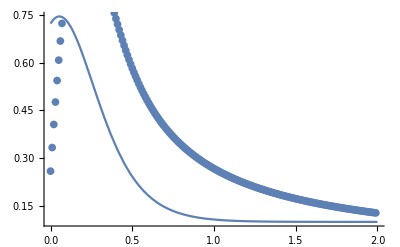

```mathematica
ic={a->1,b->4,c->0.5,d->7,g->0.1};
Show[
Plot[linearSigmoid/.ic,{Sves,0,2}],
ListPlot[dat]]
```

{a→6.05991,b→1015.16,c→-4.54209,d→4.99987,g→0.164929}

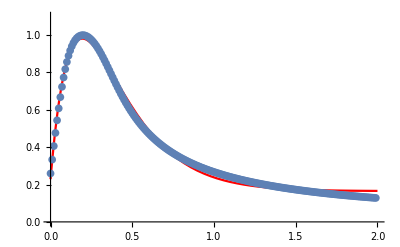

```mathematica
sol=FindFit[dat,linearSigmoid,ic/.Rule->List,Sves,Method->{"Newton"}]
Show[
Plot[linearSigmoid/.sol,{Sves,0,2},PlotStyle->Red,PlotRange->{0,1.1}],
ListPlot[dat]]
```

```mathematica
CForm[linearSigmoid]
```

g + (a + b*Sves)/(1 + Power(E,-c + d*Sves))

```mathematica
sol/.Rule[x_,v_]:>Rule[x,ScientificForm[v,3]]//ToString
```

3                                     -1
{a -> 6.06, b -> 1.02 × 10 , c -> -4.54, d -> 5., g -> 1.65 × 10  }

```mathematica
Clipboard
```

## 2-sigmoids

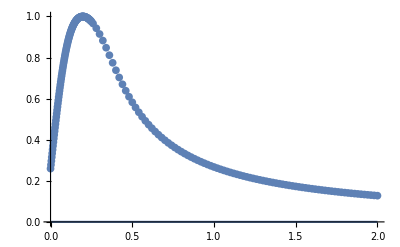

```mathematica
f=(w3/(1+Exp[w1*Smem+b1]))*(w4/(1+Exp[w2*Smem+b2]));
ic={w1->-40,w2->3,b1->0,b2->-1,w3->1.2,w4->0.0};
Show[
Plot[f/.ic,{Smem,0,2},PlotRange->{0,1}],
ListPlot[resampledData]]
```

{a→0.137277,b→14.2385,c→0.281901,d→6.25876,g→0.189442}

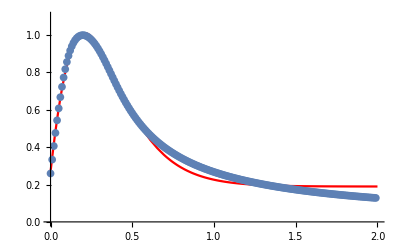

```mathematica
sol=FindFit[resampledData,f,ic/.Rule->List,Smem,Method->{"Gradient"}]
Show[
Plot[f/.sol,{Smem,0,2},PlotRange->{0,1.1},PlotStyle->Red],
ListPlot[dat]]
```

## steady state model

```mathematica
sysDE={
p1[x]==p5*grad*maxdose*(l+dX*x),
Scyto[x]'[t]==-p1[x]*Scyto[x][t]+p2*Smem[x][t]+p4*Sves[x][t]+Di[Scyto[x][t]],
Smem[x]'[t]==p1[x]*Scyto[x][t]-p2*Smem[x][t]-p3*Smem[x][t],
Sves[x]'[t]==p3*Smem[x][t]-p4*Sves[x][t],
MAPKpp[x]'[t]==funcMAPKpp[Sves[x][t]]-MAPKpp[x][t]
};
sys=sysDE/.{p3->p3[Smem[x][t]]};
sys=DeleteCases[sys,Sves[x]'[t]==_];
sys=sys/.{Sves[x][t]->Stot-Smem[x][t]-Scyto[x][t]};
sys=sys/.{{x->0},{x->1}}//Flatten;
sys=sys/.Di[Scyto[x_][t]]:>Di*(Scyto[1-x][t]-Scyto[x][t]);
sys=sys/.LHS_'[t]->0;
sys=sys/.x_[t]->x;
sys=Append[sys,MI==(MAPKpp[1]-MAPKpp[0])/(grad*maxdose*dX)];
sys//TableForm
```

p1[0]==grad l maxdose p5
0==-p1[0] Scyto[0]+Di (-Scyto[0]+Scyto[1])+p4 (Stot-Scyto[0]-Smem[0])+p2 Smem[0]
0==p1[0] Scyto[0]-p2 Smem[0]-p3[Smem[0]] Smem[0]
0==funcMAPKpp[Stot-Scyto[0]-Smem[0]]-MAPKpp[0]
p1[1]==grad (dX+l) maxdose p5
0==Di (Scyto[0]-Scyto[1])-p1[1] Scyto[1]+p4 (Stot-Scyto[1]-Smem[1])+p2 Smem[1]
0==p1[1] Scyto[1]-p2 Smem[1]-p3[Smem[1]] Smem[1]
0==funcMAPKpp[Stot-Scyto[1]-Smem[1]]-MAPKpp[1]
MI==(-MAPKpp[0]+MAPKpp[1])/(dX grad maxdose)

```mathematica
sys=sysDE[[2]];
sys=sys/.{LHS_'[t]->eqScyto[x],x_[t]->x};
sys=sys/.{{x->1},{x->2}}//Flatten;
sys=sys/.Di[Scyto[x_]]:>Di*(Scyto[3-x]-Scyto[x]);
TableForm[sys]
ToString[CForm@sys]
```

eqScyto[1]==-p1[1] Scyto[1]+Di (-Scyto[1]+Scyto[2])+p2 Smem[1]+p4 Sves[1]
eqScyto[2]==Di (Scyto[1]-Scyto[2])-p1[2] Scyto[2]+p2 Smem[2]+p4 Sves[2]

List(eqScyto(1) == -(p1(1)*Scyto(1)) + Di*(-Scyto(1) + Scyto(2)) + p2*Smem(1) + p4*Sves(1),eqScyto(2) == Di*(Scyto(1) - Scyto(2)) - p1(2)*Scyto(2) + p2*Smem(2) + p4*Sves(2))

```mathematica
params={
Stot->2,
Di->0.001,
grad->1,
maxdose->1,
p2->1,
p3[_]->1,
p4->1,
p5->1,
dX->0.001,
funcMAPKpp->Function[Sves,Evaluate[linearSigmoid/.sol]],
l->1
};
model=sys/.params;TableForm[model]
```

p1[0]==1
0==2-Scyto[0]-p1[0] Scyto[0]+0.001 (-Scyto[0]+Scyto[1])
0==p1[0] Scyto[0]-2 Smem[0]
0==0.164929-MAPKpp[0]+(6.05991+1015.16 (2-Scyto[0]-Smem[0]))/(1+ⅇ^(4.54209+4.99987 (2-Scyto[0]-Smem[0])))
p1[1]==1.001
0==2+0.001 (Scyto[0]-Scyto[1])-Scyto[1]-p1[1] Scyto[1]
0==p1[1] Scyto[1]-2 Smem[1]
0==0.164929-MAPKpp[1]+(6.05991+1015.16 (2-Scyto[1]-Smem[1]))/(1+ⅇ^(4.54209+4.99987 (2-Scyto[1]-Smem[1])))
MI==1000. (-MAPKpp[0]+MAPKpp[1])

```mathematica
stateVars=model/.Plus|Times|Equal|Power->List//Flatten//Select[#,(Not@NumericQ@#&)]&//Union
```

{MI,MAPKpp[0],MAPKpp[1],p1[0],p1[1],Scyto[0],Scyto[1],Smem[0],Smem[1]}

```mathematica
roots=FindRoot[model,Thread[{stateVars,1}]]
```

{MI→-0.106238,MAPKpp[0]→0.955497,MAPKpp[1]→0.955391,p1[0]→1.,p1[1]→1.001,Scyto[0]→0.5,Scyto[1]→0.49975,Smem[0]→0.25,Smem[1]→0.250125}

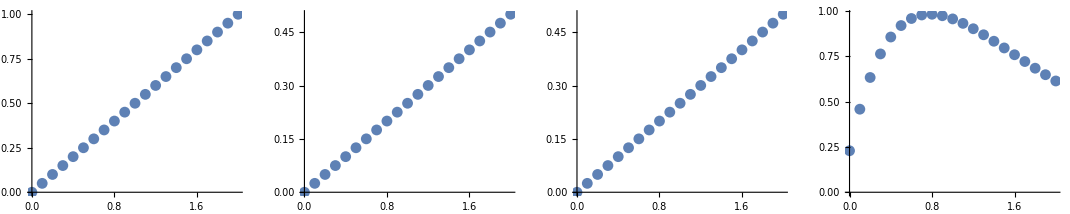

```mathematica
scaffoldResponse=Function[s,
roots=FindRoot[sys/.Stot->s/.params,Thread[{stateVars,0}]];
Append[roots,Stot->s]
]/@Range[0,2,0.1];
GraphicsRow[{
ListPlot[{Stot,Scyto[1]}/.scaffoldResponse],
ListPlot[{Stot,Smem[1]}/.scaffoldResponse],
ListPlot[{Stot,Stot-Smem[1]-Scyto[1]}/.scaffoldResponse],
ListPlot[{Stot,MAPKpp[1]}/.scaffoldResponse]}]
```

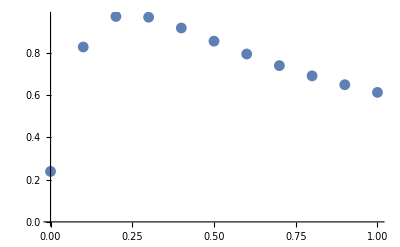

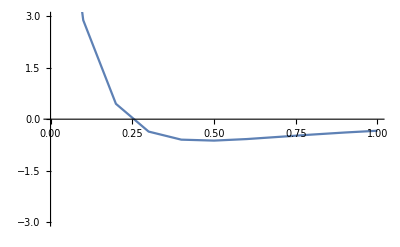

```mathematica
doseResponse=Function[len,
roots=FindRoot[sys/.l->len/.params,Thread[{stateVars,0}]];
Append[roots,l->len]
]/@Range[0,1,0.1];
ListPlot[{l,MAPKpp[1]}/.doseResponse]
ListPlot[{l,MI}/.doseResponse,PlotRange->{-3,3},Joined->True]
```

### Explicitly w.r.t p_3(·)

```mathematica
params={
Stot->2,
Di->0.001,
grad->1,
maxdose->1,
p2->1,
p4->1,
p5->1,
dX->0.001,
funcMAPKpp->Function[Sves,Evaluate[linearSigmoid/.sol]],
l->1
};
model=sys/.params;TableForm[model]
```

p1[0]==1
0==2-Scyto[0]-p1[0] Scyto[0]+0.001 (-Scyto[0]+Scyto[1])
0==p1[0] Scyto[0]-Smem[0]-p3[Smem[0]] Smem[0]
0==0.164929-MAPKpp[0]+(6.05991+1015.16 (2-Scyto[0]-Smem[0]))/(1+ⅇ^(4.54209+4.99987 (2-Scyto[0]-Smem[0])))
p1[1]==1.001
0==2+0.001 (Scyto[0]-Scyto[1])-Scyto[1]-p1[1] Scyto[1]
0==p1[1] Scyto[1]-Smem[1]-p3[Smem[1]] Smem[1]
0==0.164929-MAPKpp[1]+(6.05991+1015.16 (2-Scyto[1]-Smem[1]))/(1+ⅇ^(4.54209+4.99987 (2-Scyto[1]-Smem[1])))
MI==1000. (-MAPKpp[0]+MAPKpp[1])

```mathematica
Solve[model,
```